```mathematica
Tr = 15. (* Recombination time in Xe*)

(* For tau1 =2.2 ns, tau1 < Tr *)
I1[t_]:= (1+t/15.)^-2
```

Set::wrsym: Symbol Tr is Protected.

15.

```mathematica
(* For tau2 = 27 ns, tau2 > Tr *)
I2[t_]:=Exp[-t/27.]/27.
```

```mathematica
(* We need to normalize I1 and I2*)
```

```mathematica
Integrate[I1[t],{t,0,Infinity}]
```

15.

```mathematica
NoI1[t_]:=(1/15.)*I1[t]
```

```mathematica
Integrate[NoI1[t],{t,0,Infinity}]
```

1.

```mathematica
(* I2 is already normalized *)
```

```mathematica
Integrate[I2[t],{t,0,Infinity}]
```

1.

```mathematica
(*write down the recombination intensity *)
```

```mathematica
II[t_]:=0.44*(1./15.)*I1[t]+0.56*I2[t]
```

```mathematica
Integrate[II[t],{t,0,Infinity}]
```

1.

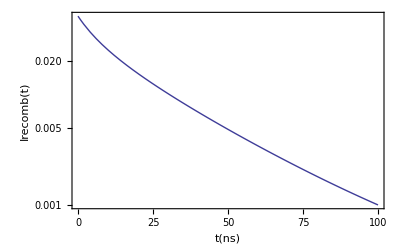

```mathematica
(* Plot the recomb intensity*)
LogPlot[II[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Irecomb(t)"}]
```

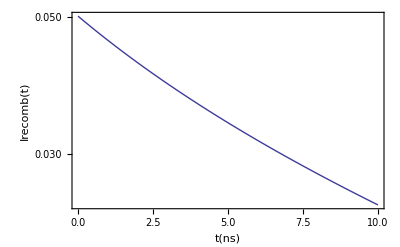

```mathematica
(* Plot the recomb intensity in the shorter range*)
LogPlot[II[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Irecomb(t)"}]
```

```mathematica
(*excitation intensity *)
```

```mathematica
SI[t_]:=0.15*Exp[-t/2.2]/2.2 + 0.85 *Exp[-t/27.]/27.
```

```mathematica
(* is normalized *)
Integrate[SI[t],{t,0,Infinity}]
```

1.

```mathematica
(* Plot the scint intensity in the shorter range*)
```

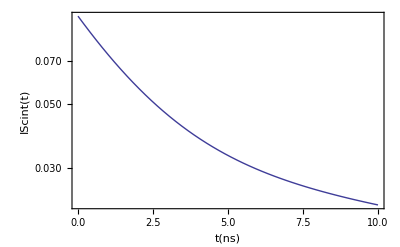

```mathematica
LogPlot[SI[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","IScint(t)"}]
```

```mathematica
(* total function *)
L[t_]:=0.7*II[t]+0.3*SI[t]
```

```mathematica
(* also normalized *)
```

```mathematica
Integrate[L[t],{t,0,Infinity}]
```

1.

```mathematica
(* multiply by the total number of photons*)
```

```mathematica
NG[t_]:=3 10^4*L[t]
```

```mathematica
Integrate[NG[t],{t,0,Infinity}]
```

30000.

```mathematica
(* plot in the short range)
```

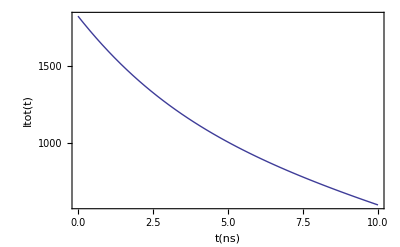

```mathematica
LogPlot[NG[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* plot in the long range *)
```

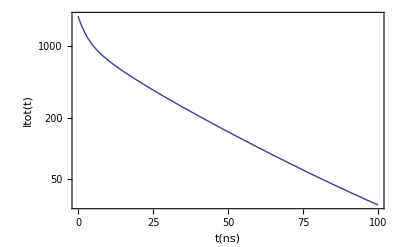

```mathematica
LogPlot[NG[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* plot in the medium range *)
```

```mathematica
LogPlot[NG[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

-Graphics-

```mathematica
(* plot in the very short range)
```

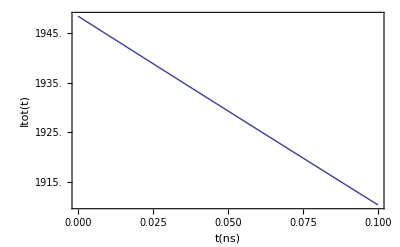

```mathematica
LogPlot[NG[t],{t,0.,0.1},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* how many photons emitted in the first 100 ps?)
```

```mathematica
tb =Table[NG[t],{t,0.,0.1,0.01}]
```

{1948.53,1944.66,1940.8,1936.96,1933.13,1929.32,1925.52,1921.74,1917.97,1914.21,1910.47}

```mathematica
Total[tb]
```

21223.3

```mathematica
(* Fit to two exponentials*)
```

```mathematica
fp=Table[{t,NG[t]},{t,0.,10.,0.05}];
```

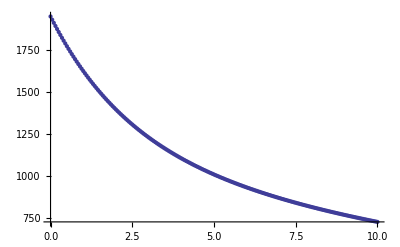

```mathematica
gp=ListPlot[fp]
```

```mathematica
model2 =a*Exp[-t/2.2]+b*Exp[-t/27.]
```

a ⅇ^(-0.454545 t)+b ⅇ^(-0.037037 t)

```mathematica
fit2 = FindFit[fp,model2,{a,b},t]
```

{a→911.082,b→1084.64}

```mathematica
modelf2=Function[{t},Evaluate[model2/.fit2]]
```

Function[{t},911.082 ⅇ^(-0.454545 t)+1084.64 ⅇ^(-0.037037 t)]

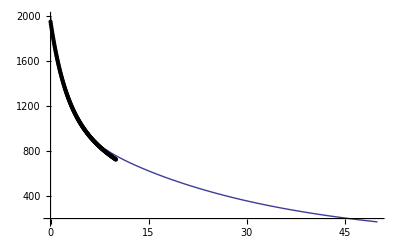

```mathematica
Plot[modelf2[t],{t,0,50},Epilog->Map[Point,fp]]
```

```mathematica
Plot[modelf2[t],{t,0,50},Epilog->Map[Point,fp2]]
```

-Graphics-

```mathematica
P1 = LogPlot[NG[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

-Graphics-

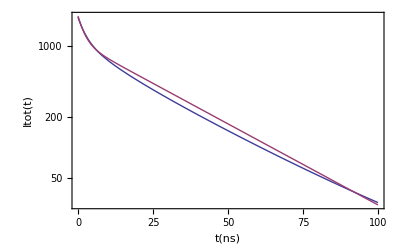

```mathematica
P2 = LogPlot[{NG[t],modelf2[t]},{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* how good is the fit at short times? *)
tb =Table[modelf2[t],{t,0.,0.1,0.01}]
```

{1995.73,1991.19,1986.68,1982.18,1977.71,1973.25,1968.81,1964.39,1959.98,1955.6,1951.23}

```mathematica
Total[tb]
```

21706.7

```mathematica
(* and in total *)
tb =Table[modelf2[t],{t,0.,100.,1.}]
```

```mathematica
Total[tb]
```

31617.3

```mathematica
model4 =a*Exp[-t/2.2]+b*Exp[-t/40.]
```

a ⅇ^(-0.454545 t)+b ⅇ^(-0.025 t)

```mathematica
fit3 = FindFit[fp,model4,{a,b},t]
```

{a→1030.81,b→995.035}

```mathematica
modelf3=Function[{t},Evaluate[model4/.fit3]]
```

Function[{t},1030.81 ⅇ^(-0.454545 t)+995.035 ⅇ^(-0.025 t)]

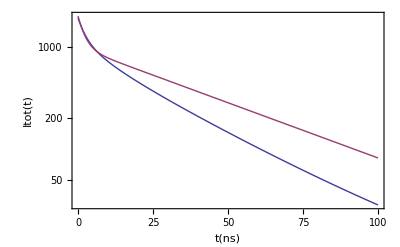

```mathematica
LogPlot[{NG[t],modelf3[t]},{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

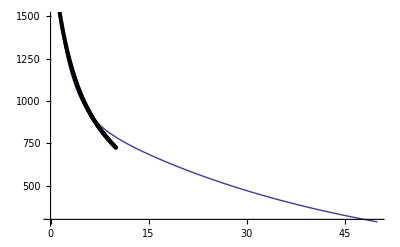

```mathematica
Plot[modelf3[t],{t,0,50},Epilog->Map[Point,fp]]
```

```mathematica
fp2=Table[{t,NG[t]},{t,0.,50.,0.05}];
```

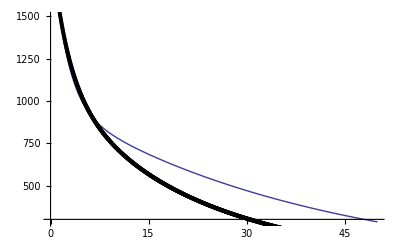

```mathematica
Plot[modelf3[t],{t,0,50},Epilog->Map[Point,fp2]]
```

```mathematica
E2[t_]:=911*2.2*Exp[-t/2.2]/2.2 + 1084*27. *Exp[-t/27.]/27.
```

```mathematica
i2 = Integrate[E2[t],{t,0,Infinity}]
```

31272.2

```mathematica
a1 = 911*2.2/i2
```

0.0640889

```mathematica
a2 = 1084*27./i2
```

0.935911

```mathematica
E3[t_]:=1031*2.2*Exp[-t/2.2]/2.2 + 995*40. *Exp[-t/40.]/40.
```

```mathematica
i3 = Integrate[E3[t],{t,0,Infinity}]
```

42068.2

```mathematica
b1 = 1031*2.2/i3
```

0.0539172

```mathematica
b2 = 995*40/i3
```

0.946083

```mathematica
A1R[x_]:=x/(1+x)
```

```mathematica
A2R[x_]:=1-A1R[x]
```

```mathematica
A1R[0.8]
```

0.444444